```mathematica
Quiet@Remove["Global`*"];
eqn = {y'[x]== 2.x y[x],  y[1] == 2*Exp[1] }
sol = DSolve[eqn, y[x], x][[1]]
res = y[x]/.First@sol
Plot[{res,10}, {x, 0, 2}, AxesLabel->{"x", "y(x)"}, PlotLabel->"Graph of y against x", PlotStyle->{Red,Thickness[0.006]},GridLines->Automatic]
```

```mathematica
x/.FindRoot[res == 10, {x,3}]
```

```mathematica
x/.FindRoot[{res==10},{x,1.0}]
```

```mathematica
x/.FindRoot[{res==10},{x,2.0}]
```

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
ClearAll[eqn, x,y, sol, res]
```

```mathematica
eqn = {y''[x] + y'[x] - 2y[x] == Exp[2x] + 2*Exp[-2x], y[0] == 5, y'[0] == 7}
sol= DSolve[eqn, y[x], x][[1]]
res = y[x]/.sol 
Plot[res, {x,0,10},PlotStyle->Blue,PlotRange->All,Frame->True,GridLines->Full]
```

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
eqn = {y'[x]==  (√x-1)y[x], y[4] == 6}
sol = DSolve[eqn, y[x], x][[1]]
res = y[x]/.First @ sol
```

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
eqn = {y'[x]== -3(y[x]-3)/x, y[-1]== 5}
Sol = DSolve[eqn, y[x], x]
result = y[x]/.First@Sol
Plot[result, {x,0,10}, PlotStyle->Blue,PlotRange->All,Frame->True,GridLines->Full]
```

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
eqn = {y''[x] +2 y'[x] +5y[x] == 0, y[0] == 0, y'[0] == 2}
sol= DSolve[eqn, y[x], x][[1]]
res = y[x]/.sol 
Plot[res, {x,0,10},PlotStyle->Blue,PlotRange->All,Frame->True,GridLines->Full]
```

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
eqn = {y''[x] -2 y'[x]== 13*Exp[3x] + 23}
sol= DSolve[eqn, y[x], x][[1]]
res = y[x]/.sol
```

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
eqns = {y1'[x] == 9y2[x], y2'[x] == -9y1[x]}
sol = DSolve[eqns, {y1[x], y2[x]},x][[1]]
y1 = y1[x]/.sol
y2 = y2[x]/.sol
```

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
eqns = {{y1'[x] == 5y1[x] -6y2[x], y2'[x] == 2y1[x] -2y2[x]}, y1[0] == 5, y2[0]== 3}
sol = DSolve[eqns, {y1[x], y2[x]},x][[1]]
y1 = y1[x]/.sol
y2 = y2[x]/.sol
Plot[{y1,y2}, {x,0,1},PlotStyle->{Blue, Red},PlotRange->All,Frame->True,GridLines->Full]
```

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
eqn = {2x +y == 4, 2x+3y == 0}
sol = Solve[eqn, {x,y}][[1]]
Print["x = "  , x/.sol, " y = "  , y/.sol]
```

```mathematica
{2 x+y==4,2 x+3 y==0}
```

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
derivative[{x_, y_}] := x + y;
xStart = 1;
yStart = 13;
xmax = 5;
initialpoints = {xStart, yStart};
nSteps = 4;
h =(xmax - xStart)/nSteps;
solDSolve = DSolve[{y'[x] == derivative[{x, y[x]}], y[xStart]==  yStart}, y[x], x][[1]]
plotDSolve = Plot[y[x]/.solDSolve, {x, xStart, xmax}, PlotStyle->{Black}];
stepEuler[{x_, y_}] := {x + h, y + h*derivative[{x, y}]};
solEuler = NestList[stepEuler, initialpoints, 4];
plotEuler = ListPlot[solEuler, PlotStyle->{Red, PointSize[0.015]}];
Show [plotDSolve, plotEuler]
```

```mathematica
ClearAll[RungeKuttaStep];
RungeKuttaStep[{x_,y_}]:=Module[
{k1,k2,k3,k4},
k1=derivative[{x,y}];
k2=derivative[{x+h/2,y+h/2*k1}];
k3=derivative[{x+h/2,y+h/2*k2}];
k4=derivative[{x+h,y+h*k3}];
{x+h,y+h/6*(k1+2k2+2k3+k4)}
];
solRunge = NestList[RungeKuttaStep, initialpoints, nSteps]
plotRunge = ListPlot[solRunge, PlotStyle->{Black, PointSize[0.015]}];
Show[ plotDSolve,plotEuler, plotRunge]
```

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
derivative[{x_, y_}] := 2x y;
xStart = 1;
xmax = 3;
yStart = 3;
nSteps = 4;
△x = h = (xmax - xStart)/nSteps;
initialpoint = {xStart, yStart};
solDSolve = DSolve[{y'[x] ==  derivative[{x, y[x]}], y[xStart] ==  yStart}, y[x], x][[1]];
PlotDSolve = Plot[y[x]/.solDSolve, {x, xStart, xmax}, PlotStyle->{Black}];
stepEuler[{x_, y_}]:= {x + △x, y + △x*derivative[{x, y}]};
solEuler = NestList[stepEuler, initialpoint, nSteps];
plotEuler = ListPlot[solEuler, PlotStyle->{Red, PointSize[0.015]}];
Show[PlotDSolve, plotEuler]
```

```mathematica
ClearAll[RungeKuttaStep];
RungeKuttaStep[{x_,y_}]:=Module[
{k1,k2,k3,k4},
k1=derivative[{x,y}];
k2=derivative[{x+h/2,y+h/2*k1}];
k3=derivative[{x+h/2,y+h/2*k2}];
k4=derivative[{x+h,y+h*k3}];
{x+h,y+h/6*(k1+2k2+2k3+k4)}
];
solRunge = NestList[RungeKuttaStep, initialpoint, nSteps]
plotRunge = ListPlot[solRunge, PlotStyle->{Black, PointSize[0.015]}];
Show[PlotDSolve, plotEuler, plotRunge]
```

```mathematica
Quiet@Remove["Global`*"]
```

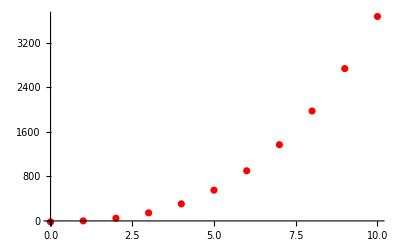

-17.332+8.8484 x+6.04866 x^2+2.99625 x^3

-17.332+8.8484 x+6.04866 x^2+2.99625 x^3

```mathematica
rn := Random[];
f[x_]:= 3 x^3 + 6 x^2 + 9x - 18;
data = Table[{x, f[x] + rn}, {x, 0, 10}];
ListPlot[data, PlotStyle->{Red}]
error[{x_, y_}]:= (y- (a x^3+b x^2 + c x + d))^2;
totalerror = Total[error/@data];
criticalpointseqns = 0 == D[totalerror, #]&/@{a, b, c,d};
criticalpoints = Solve[criticalpointseqns][[1]];
yfit = a*x^3+ b*x^2 + c x + d/.criticalpoints;
y = Fit[data, {1, x, x^2,x^3}, x];
```

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
n =20;
data = Flatten[Table[N[{x,y ,Exp[4 + Sin[5x] + Cos[7y]]}], {x, 0, 2Pi, 2Pi/n}, {y, 0, 3Pi, 3Pi/n}], 1];
int = Interpolation[data];
{{xmin, xmax} ,{ymin, ymax}}= int[[1]];
ListPlot3D[data];
```

-Graphics3D-

Plot::pllim: Range specification {{x,0.,6.28319},{y,0.,9.42478}} is not of the form {x, xmin, xmax}.

Plot[int[x,y],{{x,xmin,xmax},{y,ymin,ymax}}]

```mathematica
Quiet@Remove["Global`*"]
```

```mathematica
f[t_]:= 9 + 3 Exp[5 Sin[4t]- 9 Cos [10t]];
data = Table[N[{t,f[t]}], {t, 0, 8Pi, Pi/2000}];
y = FindFit[data, a + b * Exp[(c*Sin[d*t]-d*Cos[e*t])],{a, b, c, d, e}, t]
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→76084.9,b→6.58985,c→9.20847,d→0.491201,e→0.979952}